## fit some data with a model

### fitting model to data in 2D

```mathematica
clear:=Clear[lmf,nlm];
```

```mathematica
t=Subdivide[0,2.Pi,1000-1];
```

```mathematica
data=Thread[{t,Sin[t]+RandomReal[0.33,1000]}];
```

```mathematica
(*suppose `data` is something that we acquire from an experiment and suppose we know that something like a Sin function would fit the data *)
```

```mathematica
lmf=LinearModelFit[data,Sin[x],{x}]
```

FittedModel[0.167186+0.997645 Sin[x]]

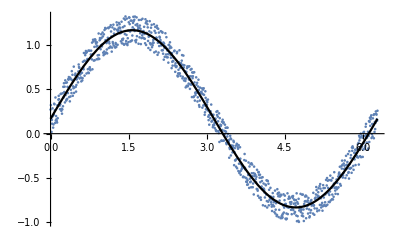

```mathematica
Show[ListPlot[data],With[{lmf=Normal[lmf]},Plot[lmf,{x,0,2Pi},PlotStyle->Black]]]
```

```mathematica
bands=lmf["SinglePredictionBands"]
```

{0.167186+0.997645 Sin[x]-1.96234 √(0.00926772+2.78612×10^-37 Sin[x]+0.0000185355 Sin[x]^2),0.167186+0.997645 Sin[x]+1.96234 √(0.00926772+2.78612×10^-37 Sin[x]+0.0000185355 Sin[x]^2)}

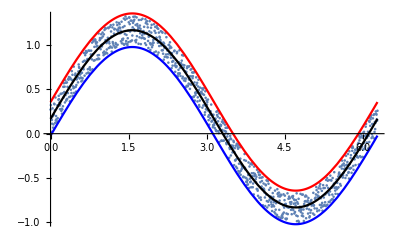

```mathematica
Show[ListPlot[data],With[{lmf=Normal[lmf]},Plot[lmf,{x,0,2Pi},PlotStyle->Black]],
Plot[bands,{x,0,2π},PlotStyle->{Blue,Red}]]
```

```mathematica
clear
```

```mathematica
nlm=NonlinearModelFit[data,{a Sin[x]+b},{a,b},x]
```

FittedModel[0.167186+0.997645 Sin[x]]

```mathematica
Show[ListPlot[data],With[{nlm=Normal[nlm]},Plot[nlm,{x,0,2Pi},PlotStyle->Black]]]
```

-Graphics-

```mathematica
bands=nlm["SinglePredictionBands"]
```

{0.167186+0.997645 Sin[x]-1.96234 √(0.00926772+1.10602×10^-21 Sin[x]+0.0000185355 Sin[x]^2),0.167186+0.997645 Sin[x]+1.96234 √(0.00926772+1.10602×10^-21 Sin[x]+0.0000185355 Sin[x]^2)}

```mathematica
Show[ListPlot[data],With[{nlm=Normal[nlm]},Plot[nlm,{x,0,2Pi},PlotStyle->Black]],
Plot[bands,{x,0,2π},PlotStyle->{Blue,Red}]]
```

-Graphics-

```mathematica
clear
```

### fitting model to data in 3D

```mathematica
(*suppose `data` is something that we acquire from an experiment and suppose we know that some model like a Sin[]Cos[] function would fit the dataset*)
```

```mathematica
data=MapAt[#+RandomReal[0.25]&,Flatten[Table[{x,y,Sin[x]Cos[y]},{x,0,5,0.1},{y,0,5,0.1}],1],{All,3}];
```

```mathematica
lmf=LinearModelFit[data,{Sin[x]Cos[y]},{x,y}]
```

FittedModel[0.122734+1.00608 Cos[y] Sin[x]]

```mathematica
plt=ListPlot3D[data,ColorFunction->"Rainbow",InterpolationOrder->10,Mesh->None]
```

-Graphics3D-

```mathematica
plt=ListPointPlot3D[data,ColorFunction->"Rainbow",PlotStyle->PointSize[0.01]]
```

-Graphics3D-

```mathematica
Show[plt,With[{lmf=Normal[lmf]},Plot3D[lmf,{x,0,5},{y,0,5},PlotStyle->{Black}]]]
```

-Graphics3D-

```mathematica
lmf["Properties"]
```

{AdjustedRSquared,AIC,AICc,ANOVATable,ANOVATableDegreesOfFreedom,ANOVATableEntries,ANOVATableFStatistics,ANOVATableMeanSquares,ANOVATablePValues,ANOVATableSumsOfSquares,BasisFunctions,BetaDifferences,BestFit,BestFitParameters,BIC,CatcherMatrix,CoefficientOfVariation,CookDistances,CorrelationMatrix,CovarianceMatrix,CovarianceRatios,Data,DesignMatrix,DurbinWatsonD,EigenstructureTable,EigenstructureTableEigenvalues,EigenstructureTableEntries,EigenstructureTableIndexes,EigenstructureTablePartitions,EstimatedVariance,FitDifferences,FitResiduals,Function,FVarianceRatios,HatDiagonal,MeanPredictionBands,MeanPredictionConfidenceIntervals,MeanPredictionConfidenceIntervalTable,MeanPredictionConfidenceIntervalTableEntries,MeanPredictionErrors,ParameterConfidenceIntervals,ParameterConfidenceIntervalTable,ParameterConfidenceIntervalTableEntries,ParameterConfidenceRegion,ParameterErrors,ParameterPValues,ParameterTable,ParameterTableEntries,ParameterTStatistics,PartialSumOfSquares,PredictedResponse,Properties,Response,RSquared,SequentialSumOfSquares,SingleDeletionVariances,SinglePredictionBands,SinglePredictionConfidenceIntervals,SinglePredictionConfidenceIntervalTable,SinglePredictionConfidenceIntervalTableEntries,SinglePredictionErrors,StandardizedResiduals,StudentizedResiduals,VarianceInflationFactors}

```mathematica
lmf["AdjustedRSquared"]
```

0.979787

```mathematica
band=lmf["SinglePredictionBands"]
```

{0.122734+1.00608 Cos[y] Sin[x]-1.96088 √(0.0051995+3.68664×10^-7 Cos[y] Sin[x]+8.03136×10^-6 Cos[y]^2 Sin[x]^2),0.122734+1.00608 Cos[y] Sin[x]+1.96088 √(0.0051995+3.68664×10^-7 Cos[y] Sin[x]+8.03136×10^-6 Cos[y]^2 Sin[x]^2)}

```mathematica
Plot3D[{band[[1]],band[[2]]},{x,0,5},{y,0,5},PlotStyle->{{Opacity[0.5],Red},{Opacity[0.5],Blue}}]
```

-Graphics3D-

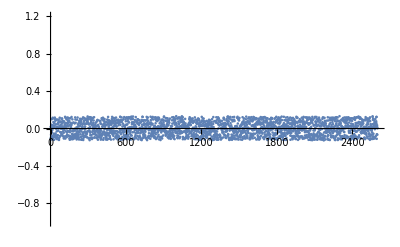

```mathematica
ListPlot[lmf["FitResiduals"],PlotRange->{-1,1.2}]
```

```mathematica
clear
```

```mathematica
nlm=NonlinearModelFit[data,a Sin[x]b Cos[y]+c,{a,b,c},{x,y},Method->"Gradient"]
```

FittedModel[0.122734+1.00608 Cos[y] Sin[x]]

```mathematica
Show[plt,With[{nlm=Normal[nlm]},Plot3D[nlm,{x,0,5},{y,0,5},PlotStyle->{Black}]]]
```

-Graphics3D-

```mathematica
clear
```